```mathematica
■Analisis MAV
```

MAV ■Analisis

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

## Cargar base de datos

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","DAX","IPC","Nikkei 225"};
```

## Fechas percentuales

```mathematica
DaysInYear[year_] := First[DateDifference[{year, 1, 1}, {year, 12, 31}]] + 1;

YearPercentual[date_] := N[QuantityMagnitude[DateDifference[DateObject[{date["Year"], 1, 1}], date]] / DaysInYear[date["Year"]]] + date["Year"];

DateFromYearPercentual[yearPercentual_] := Block[{year, daysEllapsed, date},
	year = IntegerPart[yearPercentual];
	daysEllapsed = IntegerPart[(yearPercentual - year) * DaysInYear[year]];
	date = DatePlus[DateObject[{year, 1, 1}], daysEllapsed];
	Return[date];
];
```

```mathematica
Ventana[market_,dias_]:=MovingAverage[MapAt[YearPercentual, database[[market]]["DatedPrices"], {All,1}],dias];
```

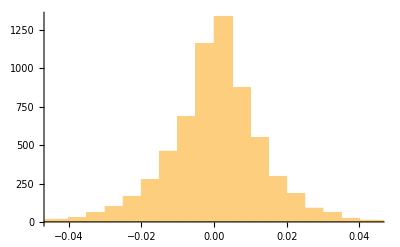

```mathematica
database[[1]]["Returns"]//Histogram
```

```mathematica
rVentana=Ventana[1,50]
```

{{1991.96,1597.36},{1991.96,1598.91},{1991.97,1600.39},{1991.97,1601.42},6410,{2017.32,12405.6},{2017.32,12422.9},{2017.32,12438.6}}
 |  |  |  |

```mathematica
MAVDates = Map[DateFromYearPercentual[#]&,rVentana[[All,1]]];
```

```mathematica
MAVPrices = rVentana[[All,2]];
MAVResult=Transpose[{MAVDates,MAVPrices}]
```

{{Day: Mon 16 Dec 1991,1597.36},{Day: Wed 18 Dec 1991,1598.91},{Day: Thu 19 Dec 1991,1600.39},6411,{Day: Wed 26 Apr 2017,12405.6},{Day: Thu 27 Apr 2017,12422.9},{Day: Sat 29 Apr 2017,12438.6}}
 |  |  |  |

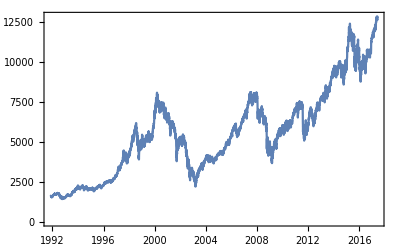

```mathematica
DateListPlot[database[[1]]["DatedPrices"]]
```

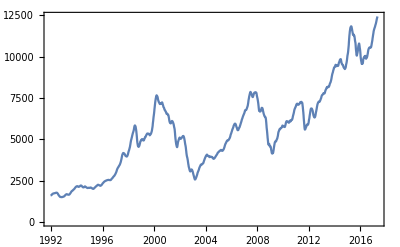

```mathematica
DateListPlot[MAVResult]
```

```mathematica
MAVDatePrice = Transpose[{MAVDates,MAVPrices}];
ReturnLogs = MAVDatePrice[[All,2]]//Returns;
DatesLogReturn = Drop[MAVDatePrice[[All,1]],-1];
```

```mathematica
MAVReturn=Transpose[{DatesLogReturn,ReturnLogs}];
```

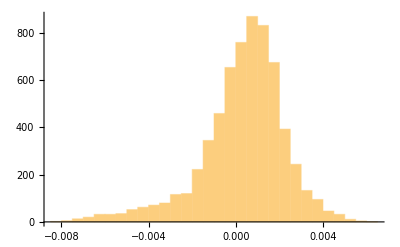

```mathematica
MAVReturn[[All,2]]//Histogram
```

```mathematica
cuartiles=Quantile[MAVReturn[[All,2]],{1/4,1/2,3/4}]
```

{-0.000556771,0.000587268,0.00151629}

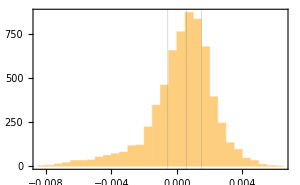

```mathematica
a=Histogram[MAVReturn[[All,2]],GridLines->{cuartiles,{}},PlotRange-> All,Frame-> True]
```

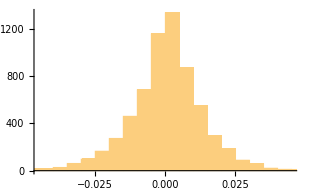

```mathematica
b=Histogram[database[[1]]["Returns"]]
```

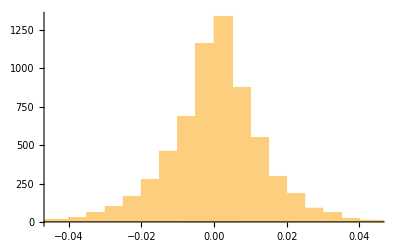

```mathematica
Show[b,a]
```

```mathematica
intervalos=Partition[Join[{-∞},cuartiles,{∞}],2,1]
```

{{-∞,-0.000556771},{-0.000556771,0.000587268},{0.000587268,0.00151629},{0.00151629,∞}}

```mathematica
discreteStates=Range[Length[intervalos]];
reglas=MapThread[(x_/;IntervalMemberQ[Interval[#1],x])->#2&,{intervalos,discreteStates}];

resultado=MAVReturn[[All,2]]/.reglas;
```

```mathematica
discretoConFechas=Transpose[{MAVReturn[[All,1]],resultado}]
```

{{Day: Mon 16 Dec 1991,3},{Day: Wed 18 Dec 1991,3},{Day: Thu 19 Dec 1991,3},{Day: Sat 21 Dec 1991,3},{Day: Mon 23 Dec 1991,3},6406,{Day: Fri 21 Apr 2017,3},{Day: Sun 23 Apr 2017,3},{Day: Mon 24 Apr 2017,3},{Day: Wed 26 Apr 2017,3},{Day: Thu 27 Apr 2017,3}}
 |  |  |  |

```mathematica
window=50;
```

```mathematica
parts=Partition[discretoConFechas,window,1];
resultado=Map[
{
Last[#[[All,1]]],
N[Entropy[#[[All,2]]]]
}&,
parts
];
```

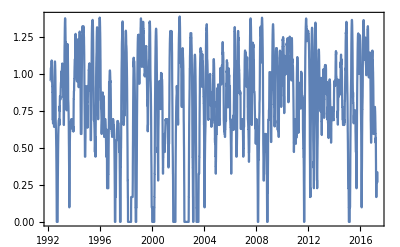

```mathematica
DateListPlot[resultado]
```